```mathematica
Directory[]
```

D:\用户目录\Documents

```mathematica
Import["combination.bmp"]
```

-Graphics-

```mathematica
list={{0,211},{109,182},{287,136},{448,117},{616,125}}
```

{{0,211},{109,182},{287,136},{448,117},{616,125}}

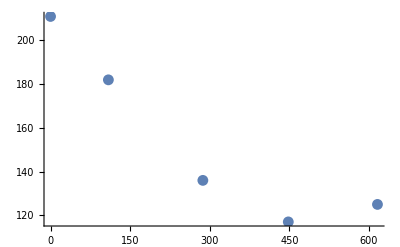

```mathematica
ListPlot[list]
```

```mathematica
NSolve[{ArcLength[Line[{list[[5]],{x,y}}]]==r,ArcLength[Line[{list[[4]],{x,y}}]]==r,ArcLength[Line[{list[[2]],{x,y}}]]==r},{x,y,r}]
```

{{x→480.481,y→1202.91,r→1086.39}}



```mathematica
Graphics[Circle[{480.48,1202.91},1086.39]]
```

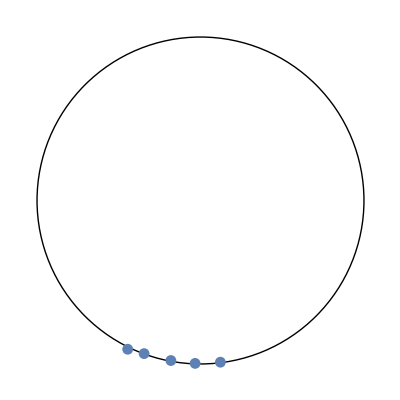

```mathematica
Show[%15,%6]
```

```mathematica
(*As the above figure shows, it seems that the ball rotates along a circle with very large radius when observed in an inertia reference frame.*)
```

```mathematica
{Subscript[V, θ]/Subscript[V, r]=(r dθ)/dr}//TraditionalForm
```

Set::write: Tag Times in V_θ/V_r is Protected.

{(dθ r)/dr}